## Firing Rate Range Calculator

### Basic Equations

f(v_in) = 1/(τ_m h(v_in))   ∍   h(v_in)=(π+2cot^-1(√(-1+2 v_in)))/(√(-1+2 v_in))
v_in= (p_qua(I_c/I_l))^2
τ_m=p_τ_m/I_l

### Creation of I_c/I_l ratio and the appropriate squared calculation

```mathematica
icilratio= Range[0.6, 1.7, 0.1]
```

{0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7}

```mathematica
icilratiosq = icilratio^2
```

{0.36,0.49,0.64,0.81,1.,1.21,1.44,1.69,1.96,2.25,2.56,2.89}

### Creation of p_qua range

```mathematica
pquas = Range[0.59124602626, 5.80848603552, 0.579693334362]
```

{0.591246,1.17094,1.75063,2.33033,2.91002,3.48971,4.06941,4.6491,5.22879,5.80849}

### Calculating v_in

```mathematica
vins=Outer[If[#1#2>0.5,#1#2,Undefined]&,pquas,icilratiosq];
TableForm[vins, TableHeadings->{pquas,icilratiosq}]
```

| 0.36 | 0.49 | 0.64 | 0.81 | 1. | 1.21 | 1.44 | 1.69 | 1.96 | 2.25 | 2.56 | 2.89
0.591246 | Undefined | Undefined | Undefined | Undefined | 0.591246 | 0.715408 | 0.851394 | 0.999206 | 1.15884 | 1.3303 | 1.51359 | 1.7087
1.17094 | Undefined | 0.57376 | 0.749401 | 0.948461 | 1.17094 | 1.41684 | 1.68615 | 1.97889 | 2.29504 | 2.63461 | 2.9976 | 3.38401
1.75063 | 0.630228 | 0.85781 | 1.1204 | 1.41801 | 1.75063 | 2.11827 | 2.52091 | 2.95857 | 3.43124 | 3.93892 | 4.48162 | 5.05933
2.33033 | 0.838917 | 1.14186 | 1.49141 | 1.88756 | 2.33033 | 2.81969 | 3.35567 | 3.93825 | 4.56744 | 5.24323 | 5.96563 | 6.73464
2.91002 | 1.04761 | 1.42591 | 1.86241 | 2.35712 | 2.91002 | 3.52112 | 4.19043 | 4.91793 | 5.70364 | 6.54754 | 7.44965 | 8.40996
3.48971 | 1.2563 | 1.70996 | 2.23342 | 2.82667 | 3.48971 | 4.22255 | 5.02519 | 5.89761 | 6.83984 | 7.85185 | 8.93366 | 10.0853
4.06941 | 1.46499 | 1.99401 | 2.60442 | 3.29622 | 4.06941 | 4.92398 | 5.85994 | 6.8773 | 7.97604 | 9.15616 | 10.4177 | 11.7606
4.6491 | 1.67368 | 2.27806 | 2.97542 | 3.76577 | 4.6491 | 5.62541 | 6.6947 | 7.85698 | 9.11223 | 10.4605 | 11.9017 | 13.4359
5.22879 | 1.88237 | 2.56211 | 3.34643 | 4.23532 | 5.22879 | 6.32684 | 7.52946 | 8.83666 | 10.2484 | 11.7648 | 13.3857 | 15.1112
5.80849 | 2.09105 | 2.84616 | 3.71743 | 4.70487 | 5.80849 | 7.02827 | 8.36422 | 9.81634 | 11.3846 | 13.0691 | 14.8697 | 16.7865

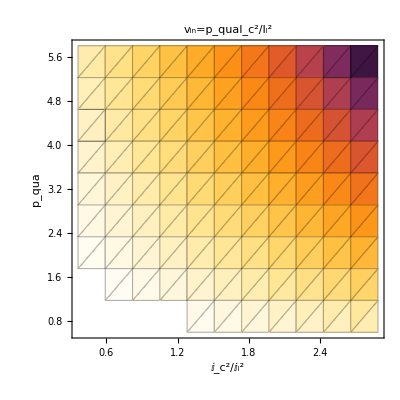

```mathematica
ListDensityPlot[vins,FrameLabel-> {(Subscript[I, c]/Subscript[I, l])^2,Subscript[p, qua]}, DataRange->{{Min[icilratiosq],Max[icilratiosq]},{Min[pquas],Max[pquas]}},PlotLabel->"v_in=p_quaI_c^2/I_l^2", ColorFunction->ColorData[{"SunsetColors", "Reverse"}], Mesh->All]
```

### Understanding h(v_in)

```mathematica
h(Subscript[v, in])=(π+2 cot^-1(√(-1+2 Subscript[v, in])))/(√(-1+2 Subscript[v, in])) ; This is the important equation repeated from above
```

```mathematica
h[vin_]:= (π+ 2ArcCot[√(2vin-1)])/(√(2vin-1))
```

Range of values for h based upon the values of v_in from above

```mathematica
hrange = h[vins];
TableForm[hrange,TableHeadings->{pquas,icilratiosq}]
```

| 0.36 | 0.49 | 0.64 | 0.81 | 1. | 1.21 | 1.44 | 1.69 | 1.96 | 2.25 | 2.56 | 2.89
0.591246 | Undefined | Undefined | Undefined | Undefined | 12.818 | 7.80284 | 5.83047 | 4.71693 | 3.98542 | 3.46214 | 3.0666 | 2.7558
1.17094 | Undefined | 14.4493 | 7.1551 | 5.03322 | 3.94156 | 3.25948 | 2.78744 | 2.43918 | 2.17064 | 1.95676 | 1.78211 | 1.63664
1.75063 | 10.4623 | 5.76743 | 4.13381 | 3.25694 | 2.69943 | 2.31026 | 2.02182 | 1.79886 | 1.62103 | 1.47572 | 1.35465 | 1.25216
2.33033 | 5.95841 | 4.04923 | 3.10812 | 2.53492 | 2.14543 | 1.86214 | 1.64621 | 1.47589 | 1.33794 | 1.22385 | 1.12787 | 1.04597
2.91002 | 4.45945 | 3.24002 | 2.56311 | 2.12681 | 1.82031 | 1.59242 | 1.41601 | 1.27523 | 1.16018 | 1.06434 | 0.983245 | 0.913712
3.48971 | 3.66455 | 2.75406 | 2.21667 | 1.85882 | 1.60226 | 1.40886 | 1.25763 | 1.13601 | 1.03603 | 0.952344 | 0.881248 | 0.820085
4.06941 | 3.15958 | 2.42425 | 1.97348 | 1.6668 | 1.44389 | 1.27422 | 1.14059 | 1.03255 | 0.943348 | 0.868418 | 0.804576 | 0.749519
4.6491 | 2.80537 | 2.18307 | 1.79158 | 1.52113 | 1.32256 | 1.17034 | 1.04982 | 0.951968 | 0.870909 | 0.80264 | 0.744342 | 0.693972
5.22879 | 2.54068 | 1.99758 | 1.64937 | 1.40604 | 1.22601 | 1.08723 | 0.976887 | 0.887013 | 0.812367 | 0.749364 | 0.695468 | 0.64883
5.80849 | 2.33398 | 1.84961 | 1.53451 | 1.31234 | 1.14694 | 1.01887 | 0.916711 | 0.833278 | 0.763833 | 0.705119 | 0.654818 | 0.611237

#### Threoretical Plot of h[v_in] and h'[v_in]

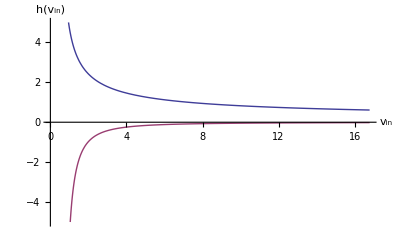

```mathematica
Plot[{h[vin], h'[vin]},{vin, 0.5, vins[[Dimensions[vins][[1]], Dimensions[vins][[2]]]]},AxesOrigin->{0,0}, PlotRange->{-5,5}, AxesLabel->{"v_in","h(v_in)"}]
```

```mathematica
h'[vin]//InputForm
```

-(1/(vin*(-1 + 2*vin))) - (Pi + 2*ArcCot[Sqrt[-1 + 2*vin]])/(-1 + 2*vin)^(3/2)

```mathematica
FindRoot[-1/(vin (-1+2 vin))-(π+2 ArcCot[√(-1+2 vin)])/(-1+2 vin)^(3/2)+1,{vin,1.5}]
```

{vin→1.97481}

#### Actual Plot of h[v_in] matrix

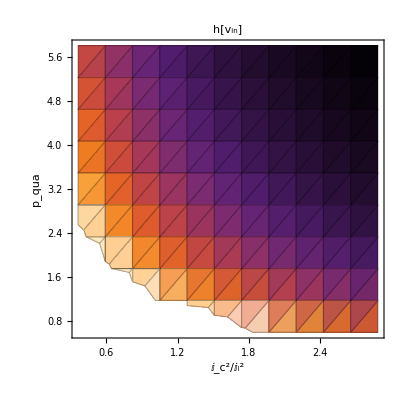

```mathematica
ListDensityPlot[hrange,FrameLabel-> {(Subscript[I, c]/Subscript[I, l])^2,Subscript[p, qua]}, DataRange->{{Min[icilratiosq],Max[icilratiosq]},{Min[pquas],Max[pquas]}},PlotLabel->"h[v_in]", ColorFunction->"SunsetColors", Mesh->All]
```

### Range of I_l parameters

```mathematica
ilrange = Range[.03, .2, .01]
```

{0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2}

```mathematica
icrange = Range[.01, .1,.01]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
icilratio
```

{0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7}

```mathematica
TableForm[Outer[Divide,icrange,ilrange],TableHeadings->{icrange,ilrange}]
```

| 0.03 | 0.04 | 0.05 | 0.06 | 0.07 | 0.08 | 0.09 | 0.1 | 0.11 | 0.12 | 0.13 | 0.14 | 0.15 | 0.16 | 0.17 | 0.18 | 0.19 | 0.2
0.01 | 0.333333 | 0.25 | 0.2 | 0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286 | 0.0666667 | 0.0625 | 0.0588235 | 0.0555556 | 0.0526316 | 0.05
0.02 | 0.666667 | 0.5 | 0.4 | 0.333333 | 0.285714 | 0.25 | 0.222222 | 0.2 | 0.181818 | 0.166667 | 0.153846 | 0.142857 | 0.133333 | 0.125 | 0.117647 | 0.111111 | 0.105263 | 0.1
0.03 | 1. | 0.75 | 0.6 | 0.5 | 0.428571 | 0.375 | 0.333333 | 0.3 | 0.272727 | 0.25 | 0.230769 | 0.214286 | 0.2 | 0.1875 | 0.176471 | 0.166667 | 0.157895 | 0.15
0.04 | 1.33333 | 1. | 0.8 | 0.666667 | 0.571429 | 0.5 | 0.444444 | 0.4 | 0.363636 | 0.333333 | 0.307692 | 0.285714 | 0.266667 | 0.25 | 0.235294 | 0.222222 | 0.210526 | 0.2
0.05 | 1.66667 | 1.25 | 1. | 0.833333 | 0.714286 | 0.625 | 0.555556 | 0.5 | 0.454545 | 0.416667 | 0.384615 | 0.357143 | 0.333333 | 0.3125 | 0.294118 | 0.277778 | 0.263158 | 0.25
0.06 | 2. | 1.5 | 1.2 | 1. | 0.857143 | 0.75 | 0.666667 | 0.6 | 0.545455 | 0.5 | 0.461538 | 0.428571 | 0.4 | 0.375 | 0.352941 | 0.333333 | 0.315789 | 0.3
0.07 | 2.33333 | 1.75 | 1.4 | 1.16667 | 1. | 0.875 | 0.777778 | 0.7 | 0.636364 | 0.583333 | 0.538462 | 0.5 | 0.466667 | 0.4375 | 0.411765 | 0.388889 | 0.368421 | 0.35
0.08 | 2.66667 | 2. | 1.6 | 1.33333 | 1.14286 | 1. | 0.888889 | 0.8 | 0.727273 | 0.666667 | 0.615385 | 0.571429 | 0.533333 | 0.5 | 0.470588 | 0.444444 | 0.421053 | 0.4
0.09 | 3. | 2.25 | 1.8 | 1.5 | 1.28571 | 1.125 | 1. | 0.9 | 0.818182 | 0.75 | 0.692308 | 0.642857 | 0.6 | 0.5625 | 0.529412 | 0.5 | 0.473684 | 0.45
0.1 | 3.33333 | 2.5 | 2. | 1.66667 | 1.42857 | 1.25 | 1.11111 | 1. | 0.909091 | 0.833333 | 0.769231 | 0.714286 | 0.666667 | 0.625 | 0.588235 | 0.555556 | 0.526316 | 0.5

### Calculate the possible range of h(v_in)/I_l

```mathematica
h[1.97481]/ilrange
```

{81.4415,61.0811,48.8649,40.7207,34.9035,30.5406,27.1472,24.4324,22.2113,20.3604,18.7942,17.4517,16.2883,15.2703,14.372,13.5736,12.8592,12.2162}

```mathematica
hiratio=Table[Simplify[hrange[[h]]/ilrange[[il]],],{h,Length[hrange]},{il,Length[ilrange]}];
TableForm[hiratio, TableHeadings->{pquas, ilrange, icilratio}]
```

| 0.03 | 0.04 | 0.05 | 0.06 | 0.07 | 0.08 | 0.09 | 0.1 | 0.11 | 0.12 | 0.13 | 0.14 | 0.15 | 0.16 | 0.17 | 0.18 | 0.19 | 0.2
0.591246 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 427.267
1.1 | 260.095
1.2 | 194.349
1.3 | 157.231
1.4 | 132.847
1.5 | 115.405
1.6 | 102.22
1.7 | 91.8598 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 320.45
1.1 | 195.071
1.2 | 145.762
1.3 | 117.923
1.4 | 99.6356
1.5 | 86.5535
1.6 | 76.665
1.7 | 68.8949 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 256.36
1.1 | 156.057
1.2 | 116.609
1.3 | 94.3386
1.4 | 79.7085
1.5 | 69.2428
1.6 | 61.332
1.7 | 55.1159 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 213.633
1.1 | 130.047
1.2 | 97.1746
1.3 | 78.6155
1.4 | 66.4237
1.5 | 57.7024
1.6 | 51.11
1.7 | 45.9299 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 183.114
1.1 | 111.469
1.2 | 83.2925
1.3 | 67.3847
1.4 | 56.9346
1.5 | 49.4592
1.6 | 43.8086
1.7 | 39.3685 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 160.225
1.1 | 97.5355
1.2 | 72.8809
1.3 | 58.9616
1.4 | 49.8178
1.5 | 43.2768
1.6 | 38.3325
1.7 | 34.4474 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 142.422
1.1 | 86.6982
1.2 | 64.783
1.3 | 52.4104
1.4 | 44.2825
1.5 | 38.4682
1.6 | 34.0733
1.7 | 30.6199 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 128.18
1.1 | 78.0284
1.2 | 58.3047
1.3 | 47.1693
1.4 | 39.8542
1.5 | 34.6214
1.6 | 30.666
1.7 | 27.558 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 116.527
1.1 | 70.9349
1.2 | 53.0043
1.3 | 42.8812
1.4 | 36.2311
1.5 | 31.474
1.6 | 27.8782
1.7 | 25.0527 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 106.817
1.1 | 65.0236
1.2 | 48.5873
1.3 | 39.3078
1.4 | 33.2119
1.5 | 28.8512
1.6 | 25.555
1.7 | 22.965 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 98.6
1.1 | 60.0218
1.2 | 44.8498
1.3 | 36.2841
1.4 | 30.6571
1.5 | 26.6319
1.6 | 23.5892
1.7 | 21.1984 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 91.5572
1.1 | 55.7346
1.2 | 41.6462
1.3 | 33.6924
1.4 | 28.4673
1.5 | 24.7296
1.6 | 21.9043
1.7 | 19.6843 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 85.4534
1.1 | 52.0189
1.2 | 38.8698
1.3 | 31.4462
1.4 | 26.5695
1.5 | 23.0809
1.6 | 20.444
1.7 | 18.372 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 80.1125
1.1 | 48.7677
1.2 | 36.4405
1.3 | 29.4808
1.4 | 24.9089
1.5 | 21.6384
1.6 | 19.1662
1.7 | 17.2237 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 75.4
1.1 | 45.899
1.2 | 34.2969
1.3 | 27.7467
1.4 | 23.4437
1.5 | 20.3655
1.6 | 18.0388
1.7 | 16.2106 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 71.2111
1.1 | 43.3491
1.2 | 32.3915
1.3 | 26.2052
1.4 | 22.1412
1.5 | 19.2341
1.6 | 17.0367
1.7 | 15.31 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 67.4632
1.1 | 41.0676
1.2 | 30.6867
1.3 | 24.826
1.4 | 20.9759
1.5 | 18.2218
1.6 | 16.14
1.7 | 14.5042 | 0.6 | Undefined
0.7 | Undefined
0.8 | Undefined
0.9 | Undefined
1. | 64.09
1.1 | 39.0142
1.2 | 29.1524
1.3 | 23.5847
1.4 | 19.9271
1.5 | 17.3107
1.6 | 15.333
1.7 | 13.779
1.17094 | 0.6 | Undefined
0.7 | 481.645
0.8 | 238.503
0.9 | 167.774
1. | 131.385
1.1 | 108.649
1.2 | 92.9146
1.3 | 81.3059
1.4 | 72.3548
1.5 | 65.2255
1.6 | 59.4038
1.7 | 54.5548 | 0.6 | Undefined
0.7 | 361.234
0.8 | 178.877
0.9 | 125.83
1. | 98.5389
1.1 | 81.487
1.2 | 69.686
1.3 | 60.9794
1.4 | 54.2661
1.5 | 48.9191
1.6 | 44.5528
1.7 | 40.9161 | 0.6 | Undefined
0.7 | 288.987
0.8 | 143.102
0.9 | 100.664
1. | 78.8312
1.1 | 65.1896
1.2 | 55.7488
1.3 | 48.7835
1.4 | 43.4129
1.5 | 39.1353
1.6 | 35.6423
1.7 | 32.7329 | 0.6 | Undefined
0.7 | 240.822
0.8 | 119.252
0.9 | 83.8869
1. | 65.6926
1.1 | 54.3247
1.2 | 46.4573
1.3 | 40.6529
1.4 | 36.1774
1.5 | 32.6127
1.6 | 29.7019
1.7 | 27.2774 | 0.6 | Undefined
0.7 | 206.419
0.8 | 102.216
0.9 | 71.9031
1. | 56.308
1.1 | 46.564
1.2 | 39.8206
1.3 | 34.8454
1.4 | 31.0092
1.5 | 27.9538
1.6 | 25.4588
1.7 | 23.3806 | 0.6 | Undefined
0.7 | 180.617
0.8 | 89.4387
0.9 | 62.9152
1. | 49.2695
1.1 | 40.7435
1.2 | 34.843
1.3 | 30.4897
1.4 | 27.1331
1.5 | 24.4596
1.6 | 22.2764
1.7 | 20.458 | 0.6 | Undefined
0.7 | 160.548
0.8 | 79.5011
0.9 | 55.9246
1. | 43.7951
1.1 | 36.2165
1.2 | 30.9715
1.3 | 27.102
1.4 | 24.1183
1.5 | 21.7418
1.6 | 19.8013
1.7 | 18.1849 | 0.6 | Undefined
0.7 | 144.493
0.8 | 71.551
0.9 | 50.3322
1. | 39.4156
1.1 | 32.5948
1.2 | 27.8744
1.3 | 24.3918
1.4 | 21.7064
1.5 | 19.5676
1.6 | 17.8211
1.7 | 16.3664 | 0.6 | Undefined
0.7 | 131.358
0.8 | 65.0464
0.9 | 45.7565
1. | 35.8323
1.1 | 29.6317
1.2 | 25.3404
1.3 | 22.1743
1.4 | 19.7331
1.5 | 17.7888
1.6 | 16.201
1.7 | 14.8786 | 0.6 | Undefined
0.7 | 120.411
0.8 | 59.6258
0.9 | 41.9435
1. | 32.8463
1.1 | 27.1623
1.2 | 23.2287
1.3 | 20.3265
1.4 | 18.0887
1.5 | 16.3064
1.6 | 14.8509
1.7 | 13.6387 | 0.6 | Undefined
0.7 | 111.149
0.8 | 55.0392
0.9 | 38.717
1. | 30.3197
1.1 | 25.0729
1.2 | 21.4418
1.3 | 18.7629
1.4 | 16.6973
1.5 | 15.052
1.6 | 13.7086
1.7 | 12.5896 | 0.6 | Undefined
0.7 | 103.21
0.8 | 51.1079
0.9 | 35.9515
1. | 28.154
1.1 | 23.282
1.2 | 19.9103
1.3 | 17.4227
1.4 | 15.5046
1.5 | 13.9769
1.6 | 12.7294
1.7 | 11.6903 | 0.6 | Undefined
0.7 | 96.329
0.8 | 47.7007
0.9 | 33.5548
1. | 26.2771
1.1 | 21.7299
1.2 | 18.5829
1.3 | 16.2612
1.4 | 14.471
1.5 | 13.0451
1.6 | 11.8808
1.7 | 10.911 | 0.6 | Undefined
0.7 | 90.3084
0.8 | 44.7194
0.9 | 31.4576
1. | 24.6347
1.1 | 20.3718
1.2 | 17.4215
1.3 | 15.2448
1.4 | 13.5665
1.5 | 12.2298
1.6 | 11.1382
1.7 | 10.229 | 0.6 | Undefined
0.7 | 84.9962
0.8 | 42.0888
0.9 | 29.6072
1. | 23.1856
1.1 | 19.1734
1.2 | 16.3967
1.3 | 14.3481
1.4 | 12.7685
1.5 | 11.5104
1.6 | 10.483
1.7 | 9.62731 | 0.6 | Undefined
0.7 | 80.2741
0.8 | 39.7506
0.9 | 27.9623
1. | 21.8975
1.1 | 18.1082
1.2 | 15.4858
1.3 | 13.551
1.4 | 12.0591
1.5 | 10.8709
1.6 | 9.90063
1.7 | 9.09246 | 0.6 | Undefined
0.7 | 76.0492
0.8 | 37.6584
0.9 | 26.4906
1. | 20.745
1.1 | 17.1552
1.2 | 14.6707
1.3 | 12.8378
1.4 | 11.4244
1.5 | 10.2988
1.6 | 9.37955
1.7 | 8.61391 | 0.6 | Undefined
0.7 | 72.2467
0.8 | 35.7755
0.9 | 25.1661
1. | 19.7078
1.1 | 16.2974
1.2 | 13.9372
1.3 | 12.1959
1.4 | 10.8532
1.5 | 9.78382
1.6 | 8.91057
1.7 | 8.18322
1.75063 | 0.6 | 348.742
0.7 | 192.248
0.8 | 137.794
0.9 | 108.565
1. | 89.9809
1.1 | 77.0087
1.2 | 67.3942
1.3 | 59.962
1.4 | 54.0344
1.5 | 49.1906
1.6 | 45.155
1.7 | 41.7388 | 0.6 | 261.557
0.7 | 144.186
0.8 | 103.345
0.9 | 81.4235
1. | 67.4857
1.1 | 57.7565
1.2 | 50.5456
1.3 | 44.9715
1.4 | 40.5258
1.5 | 36.893
1.6 | 33.8662
1.7 | 31.3041 | 0.6 | 209.245
0.7 | 115.349
0.8 | 82.6761
0.9 | 65.1388
1. | 53.9885
1.1 | 46.2052
1.2 | 40.4365
1.3 | 35.9772
1.4 | 32.4206
1.5 | 29.5144
1.6 | 27.093
1.7 | 25.0433 | 0.6 | 174.371
0.7 | 96.1238
0.8 | 68.8968
0.9 | 54.2824
1. | 44.9905
1.1 | 38.5044
1.2 | 33.6971
1.3 | 29.981
1.4 | 27.0172
1.5 | 24.5953
1.6 | 22.5775
1.7 | 20.8694 | 0.6 | 149.461
0.7 | 82.3918
0.8 | 59.0544
0.9 | 46.5277
1. | 38.5632
1.1 | 33.0037
1.2 | 28.8832
1.3 | 25.698
1.4 | 23.1576
1.5 | 21.0817
1.6 | 19.3521
1.7 | 17.8881 | 0.6 | 130.778
0.7 | 72.0928
0.8 | 51.6726
0.9 | 40.7118
1. | 33.7428
1.1 | 28.8783
1.2 | 25.2728
1.3 | 22.4858
1.4 | 20.2629
1.5 | 18.4465
1.6 | 16.9331
1.7 | 15.6521 | 0.6 | 116.247
0.7 | 64.0825
0.8 | 45.9312
0.9 | 36.1882
1. | 29.9936
1.1 | 25.6696
1.2 | 22.4647
1.3 | 19.9873
1.4 | 18.0115
1.5 | 16.3969
1.6 | 15.0517
1.7 | 13.9129 | 0.6 | 104.623
0.7 | 57.6743
0.8 | 41.3381
0.9 | 32.5694
1. | 26.9943
1.1 | 23.1026
1.2 | 20.2182
1.3 | 17.9886
1.4 | 16.2103
1.5 | 14.7572
1.6 | 13.5465
1.7 | 12.5216 | 0.6 | 95.1115
0.7 | 52.4312
0.8 | 37.5801
0.9 | 29.6086
1. | 24.5402
1.1 | 21.0024
1.2 | 18.3802
1.3 | 16.3533
1.4 | 14.7367
1.5 | 13.4156
1.6 | 12.315
1.7 | 11.3833 | 0.6 | 87.1855
0.7 | 48.0619
0.8 | 34.4484
0.9 | 27.1412
1. | 22.4952
1.1 | 19.2522
1.2 | 16.8485
1.3 | 14.9905
1.4 | 13.5086
1.5 | 12.2977
1.6 | 11.2887
1.7 | 10.4347 | 0.6 | 80.479
0.7 | 44.3648
0.8 | 31.7985
0.9 | 25.0534
1. | 20.7648
1.1 | 17.7712
1.2 | 15.5525
1.3 | 13.8374
1.4 | 12.4695
1.5 | 11.3517
1.6 | 10.4204
1.7 | 9.63203 | 0.6 | 74.7305
0.7 | 41.1959
0.8 | 29.5272
0.9 | 23.2639
1. | 19.2816
1.1 | 16.5019
1.2 | 14.4416
1.3 | 12.849
1.4 | 11.5788
1.5 | 10.5408
1.6 | 9.67607
1.7 | 8.94403 | 0.6 | 69.7484
0.7 | 38.4495
0.8 | 27.5587
0.9 | 21.7129
1. | 17.9962
1.1 | 15.4017
1.2 | 13.4788
1.3 | 11.9924
1.4 | 10.8069
1.5 | 9.83812
1.6 | 9.031
1.7 | 8.34776 | 0.6 | 65.3892
0.7 | 36.0464
0.8 | 25.8363
0.9 | 20.3559
1. | 16.8714
1.1 | 14.4391
1.2 | 12.6364
1.3 | 11.2429
1.4 | 10.1314
1.5 | 9.22324
1.6 | 8.46656
1.7 | 7.82603 | 0.6 | 61.5427
0.7 | 33.926
0.8 | 24.3165
0.9 | 19.1585
1. | 15.879
1.1 | 13.5898
1.2 | 11.8931
1.3 | 10.5815
1.4 | 9.53548
1.5 | 8.6807
1.6 | 7.96853
1.7 | 7.36567 | 0.6 | 58.1237
0.7 | 32.0413
0.8 | 22.9656
0.9 | 18.0941
1. | 14.9968
1.1 | 12.8348
1.2 | 11.2324
1.3 | 9.99367
1.4 | 9.00573
1.5 | 8.19844
1.6 | 7.52583
1.7 | 6.95647 | 0.6 | 55.0646
0.7 | 30.3549
0.8 | 21.7569
0.9 | 17.1418
1. | 14.2075
1.1 | 12.1593
1.2 | 10.6412
1.3 | 9.46769
1.4 | 8.53175
1.5 | 7.76694
1.6 | 7.12974
1.7 | 6.59034 | 0.6 | 52.3113
0.7 | 28.8371
0.8 | 20.669
0.9 | 16.2847
1. | 13.4971
1.1 | 11.5513
1.2 | 10.1091
1.3 | 8.99431
1.4 | 8.10516
1.5 | 7.37859
1.6 | 6.77325
1.7 | 6.26082
2.33033 | 0.6 | 198.614
0.7 | 134.974
0.8 | 103.604
0.9 | 84.4974
1. | 71.5144
1.1 | 62.0713
1.2 | 54.8738
1.3 | 49.1963
1.4 | 44.598
1.5 | 40.795
1.6 | 37.5956
1.7 | 34.8657 | 0.6 | 148.96
0.7 | 101.231
0.8 | 77.703
0.9 | 63.373
1. | 53.6358
1.1 | 46.5535
1.2 | 41.1554
1.3 | 36.8972
1.4 | 33.4485
1.5 | 30.5962
1.6 | 28.1967
1.7 | 26.1493 | 0.6 | 119.168
0.7 | 80.9846
0.8 | 62.1624
0.9 | 50.6984
1. | 42.9086
1.1 | 37.2428
1.2 | 32.9243
1.3 | 29.5178
1.4 | 26.7588
1.5 | 24.477
1.6 | 22.5574
1.7 | 20.9194 | 0.6 | 99.3068
0.7 | 67.4872
0.8 | 51.802
0.9 | 42.2487
1. | 35.7572
1.1 | 31.0356
1.2 | 27.4369
1.3 | 24.5981
1.4 | 22.299
1.5 | 20.3975
1.6 | 18.7978
1.7 | 17.4329 | 0.6 | 85.1201
0.7 | 57.8461
0.8 | 44.4017
0.9 | 36.2132
1. | 30.649
1.1 | 26.602
1.2 | 23.5174
1.3 | 21.0841
1.4 | 19.1134
1.5 | 17.4836
1.6 | 16.1124
1.7 | 14.9425 | 0.6 | 74.4801
0.7 | 50.6154
0.8 | 38.8515
0.9 | 31.6865
1. | 26.8179
1.1 | 23.2767
1.2 | 20.5777
1.3 | 18.4486
1.4 | 16.7242
1.5 | 15.2981
1.6 | 14.0984
1.7 | 13.0746 | 0.6 | 66.2045
0.7 | 44.9914
0.8 | 34.5347
0.9 | 28.1658
1. | 23.8381
1.1 | 20.6904
1.2 | 18.2913
1.3 | 16.3988
1.4 | 14.866
1.5 | 13.5983
1.6 | 12.5319
1.7 | 11.6219 | 0.6 | 59.5841
0.7 | 40.4923
0.8 | 31.0812
0.9 | 25.3492
1. | 21.4543
1.1 | 18.6214
1.2 | 16.4621
1.3 | 14.7589
1.4 | 13.3794
1.5 | 12.2385
1.6 | 11.2787
1.7 | 10.4597 | 0.6 | 54.1674
0.7 | 36.8112
0.8 | 28.2556
0.9 | 23.0447
1. | 19.5039
1.1 | 16.9285
1.2 | 14.9656
1.3 | 13.4172
1.4 | 12.1631
1.5 | 11.1259
1.6 | 10.2534
1.7 | 9.50884 | 0.6 | 49.6534
0.7 | 33.7436
0.8 | 25.901
0.9 | 21.1243
1. | 17.8786
1.1 | 15.5178
1.2 | 13.7185
1.3 | 12.2991
1.4 | 11.1495
1.5 | 10.1987
1.6 | 9.39891
1.7 | 8.71643 | 0.6 | 45.8339
0.7 | 31.1479
0.8 | 23.9086
0.9 | 19.4994
1. | 16.5033
1.1 | 14.3241
1.2 | 12.6632
1.3 | 11.353
1.4 | 10.2918
1.5 | 9.41422
1.6 | 8.67591
1.7 | 8.04594 | 0.6 | 42.5601
0.7 | 28.9231
0.8 | 22.2009
0.9 | 18.1066
1. | 15.3245
1.1 | 13.301
1.2 | 11.7587
1.3 | 10.5421
1.4 | 9.5567
1.5 | 8.74178
1.6 | 8.05621
1.7 | 7.47123 | 0.6 | 39.7227
0.7 | 26.9949
0.8 | 20.7208
0.9 | 16.8995
1. | 14.3029
1.1 | 12.4143
1.2 | 10.9748
1.3 | 9.83925
1.4 | 8.91959
1.5 | 8.15899
1.6 | 7.51913
1.7 | 6.97315 | 0.6 | 37.2401
0.7 | 25.3077
0.8 | 19.4257
0.9 | 15.8433
1. | 13.4089
1.1 | 11.6384
1.2 | 10.2888
1.3 | 9.2243
1.4 | 8.36212
1.5 | 7.64905
1.6 | 7.04918
1.7 | 6.53732 | 0.6 | 35.0495
0.7 | 23.819
0.8 | 18.2831
0.9 | 14.9113
1. | 12.6202
1.1 | 10.9538
1.2 | 9.68362
1.3 | 8.68169
1.4 | 7.87023
1.5 | 7.19911
1.6 | 6.63452
1.7 | 6.15278 | 0.6 | 33.1023
0.7 | 22.4957
0.8 | 17.2673
0.9 | 14.0829
1. | 11.9191
1.1 | 10.3452
1.2 | 9.14564
1.3 | 8.19938
1.4 | 7.43299
1.5 | 6.79916
1.6 | 6.26594
1.7 | 5.81096 | 0.6 | 31.36
0.7 | 21.3117
0.8 | 16.3585
0.9 | 13.3417
1. | 11.2917
1.1 | 9.80073
1.2 | 8.66429
1.3 | 7.76783
1.4 | 7.04178
1.5 | 6.44131
1.6 | 5.93615
1.7 | 5.50512 | 0.6 | 29.792
0.7 | 20.2461
0.8 | 15.5406
0.9 | 12.6746
1. | 10.7272
1.1 | 9.31069
1.2 | 8.23107
1.3 | 7.37944
1.4 | 6.68969
1.5 | 6.11924
1.6 | 5.63934
1.7 | 5.22986
2.91002 | 0.6 | 148.648
0.7 | 108.001
0.8 | 85.4371
0.9 | 70.8937
1. | 60.6769
1.1 | 53.0808
1.2 | 47.2004
1.3 | 42.5076
1.4 | 38.6725
1.5 | 35.478
1.6 | 32.7748
1.7 | 30.4571 | 0.6 | 111.486
0.7 | 81.0004
0.8 | 64.0778
0.9 | 53.1703
1. | 45.5076
1.1 | 39.8106
1.2 | 35.4003
1.3 | 31.8807
1.4 | 29.0044
1.5 | 26.6085
1.6 | 24.5811
1.7 | 22.8428 | 0.6 | 89.1891
0.7 | 64.8003
0.8 | 51.2623
0.9 | 42.5362
1. | 36.4061
1.1 | 31.8485
1.2 | 28.3202
1.3 | 25.5045
1.4 | 23.2035
1.5 | 21.2868
1.6 | 19.6649
1.7 | 18.2742 | 0.6 | 74.3242
0.7 | 54.0003
0.8 | 42.7186
0.9 | 35.4469
1. | 30.3384
1.1 | 26.5404
1.2 | 23.6002
1.3 | 21.2538
1.4 | 19.3363
1.5 | 17.739
1.6 | 16.3874
1.7 | 15.2285 | 0.6 | 63.7065
0.7 | 46.286
0.8 | 36.6159
0.9 | 30.383
1. | 26.0044
1.1 | 22.7489
1.2 | 20.2287
1.3 | 18.2175
1.4 | 16.5739
1.5 | 15.2049
1.6 | 14.0464
1.7 | 13.053 | 0.6 | 55.7432
0.7 | 40.5002
0.8 | 32.0389
0.9 | 26.5851
1. | 22.7538
1.1 | 19.9053
1.2 | 17.7001
1.3 | 15.9403
1.4 | 14.5022
1.5 | 13.3043
1.6 | 12.2906
1.7 | 11.4214 | 0.6 | 49.5495
0.7 | 36.0002
0.8 | 28.479
0.9 | 23.6312
1. | 20.2256
1.1 | 17.6936
1.2 | 15.7335
1.3 | 14.1692
1.4 | 12.8908
1.5 | 11.826
1.6 | 10.9249
1.7 | 10.1524 | 0.6 | 44.5945
0.7 | 32.4002
0.8 | 25.6311
0.9 | 21.2681
1. | 18.2031
1.1 | 15.9242
1.2 | 14.1601
1.3 | 12.7523
1.4 | 11.6018
1.5 | 10.6434
1.6 | 9.83245
1.7 | 9.13712 | 0.6 | 40.5405
0.7 | 29.4547
0.8 | 23.301
0.9 | 19.3347
1. | 16.5482
1.1 | 14.4766
1.2 | 12.8728
1.3 | 11.593
1.4 | 10.5471
1.5 | 9.67582
1.6 | 8.93859
1.7 | 8.30647 | 0.6 | 37.1621
0.7 | 27.0001
0.8 | 21.3593
0.9 | 17.7234
1. | 15.1692
1.1 | 13.2702
1.2 | 11.8001
1.3 | 10.6269
1.4 | 9.66814
1.5 | 8.8695
1.6 | 8.19371
1.7 | 7.61426 | 0.6 | 34.3035
0.7 | 24.9232
0.8 | 19.7163
0.9 | 16.3601
1. | 14.0024
1.1 | 12.2494
1.2 | 10.8924
1.3 | 9.80944
1.4 | 8.92443
1.5 | 8.18724
1.6 | 7.56342
1.7 | 7.02855 | 0.6 | 31.8532
0.7 | 23.143
0.8 | 18.308
0.9 | 15.1915
1. | 13.0022
1.1 | 11.3745
1.2 | 10.1144
1.3 | 9.10876
1.4 | 8.28697
1.5 | 7.60243
1.6 | 7.02318
1.7 | 6.52651 | 0.6 | 29.7297
0.7 | 21.6001
0.8 | 17.0874
0.9 | 14.1787
1. | 12.1354
1.1 | 10.6162
1.2 | 9.44007
1.3 | 8.50151
1.4 | 7.73451
1.5 | 7.0956
1.6 | 6.55497
1.7 | 6.09141 | 0.6 | 27.8716
0.7 | 20.2501
0.8 | 16.0195
0.9 | 13.2926
1. | 11.3769
1.1 | 9.95265
1.2 | 8.85007
1.3 | 7.97017
1.4 | 7.2511
1.5 | 6.65213
1.6 | 6.14528
1.7 | 5.7107 | 0.6 | 26.2321
0.7 | 19.0589
0.8 | 15.0771
0.9 | 12.5107
1. | 10.7077
1.1 | 9.3672
1.2 | 8.32947
1.3 | 7.50134
1.4 | 6.82457
1.5 | 6.26083
1.6 | 5.78379
1.7 | 5.37477 | 0.6 | 24.7747
0.7 | 18.0001
0.8 | 14.2395
0.9 | 11.8156
1. | 10.1128
1.1 | 8.8468
1.2 | 7.86673
1.3 | 7.08459
1.4 | 6.44542
1.5 | 5.913
1.6 | 5.46247
1.7 | 5.07618 | 0.6 | 23.4708
0.7 | 17.0527
0.8 | 13.4901
0.9 | 11.1937
1. | 9.58056
1.1 | 8.38118
1.2 | 7.45269
1.3 | 6.71172
1.4 | 6.10619
1.5 | 5.60179
1.6 | 5.17497
1.7 | 4.80901 | 0.6 | 22.2973
0.7 | 16.2001
0.8 | 12.8156
0.9 | 10.6341
1. | 9.10153
1.1 | 7.96212
1.2 | 7.08005
1.3 | 6.37614
1.4 | 5.80088
1.5 | 5.3217
1.6 | 4.91623
1.7 | 4.56856
3.48971 | 0.6 | 122.152
0.7 | 91.8019
0.8 | 73.8891
0.9 | 61.9605
1. | 53.4087
1.1 | 46.962
1.2 | 41.9209
1.3 | 37.8671
1.4 | 34.5343
1.5 | 31.7448
1.6 | 29.3749
1.7 | 27.3362 | 0.6 | 91.6137
0.7 | 68.8514
0.8 | 55.4169
0.9 | 46.4704
1. | 40.0565
1.1 | 35.2215
1.2 | 31.4406
1.3 | 28.4003
1.4 | 25.9008
1.5 | 23.8086
1.6 | 22.0312
1.7 | 20.5021 | 0.6 | 73.291
0.7 | 55.0812
0.8 | 44.3335
0.9 | 37.1763
1. | 32.0452
1.1 | 28.1772
1.2 | 25.1525
1.3 | 22.7202
1.4 | 20.7206
1.5 | 19.0469
1.6 | 17.625
1.7 | 16.4017 | 0.6 | 61.0758
0.7 | 45.901
0.8 | 36.9446
0.9 | 30.9803
1. | 26.7044
1.1 | 23.481
1.2 | 20.9604
1.3 | 18.9335
1.4 | 17.2672
1.5 | 15.8724
1.6 | 14.6875
1.7 | 13.6681 | 0.6 | 52.3507
0.7 | 39.3437
0.8 | 31.6668
0.9 | 26.5545
1. | 22.8895
1.1 | 20.1266
1.2 | 17.9661
1.3 | 16.2287
1.4 | 14.8004
1.5 | 13.6049
1.6 | 12.5893
1.7 | 11.7155 | 0.6 | 45.8069
0.7 | 34.4257
0.8 | 27.7084
0.9 | 23.2352
1. | 20.0283
1.1 | 17.6107
1.2 | 15.7203
1.3 | 14.2002
1.4 | 12.9504
1.5 | 11.9043
1.6 | 11.0156
1.7 | 10.2511 | 0.6 | 40.7172
0.7 | 30.6006
0.8 | 24.6297
0.9 | 20.6535
1. | 17.8029
1.1 | 15.654
1.2 | 13.9736
1.3 | 12.6224
1.4 | 11.5114
1.5 | 10.5816
1.6 | 9.79164
1.7 | 9.11206 | 0.6 | 36.6455
0.7 | 27.5406
0.8 | 22.1667
0.9 | 18.5882
1. | 16.0226
1.1 | 14.0886
1.2 | 12.5763
1.3 | 11.3601
1.4 | 10.3603
1.5 | 9.52344
1.6 | 8.81248
1.7 | 8.20085 | 0.6 | 33.3141
0.7 | 25.0369
0.8 | 20.1516
0.9 | 16.8983
1. | 14.566
1.1 | 12.8078
1.2 | 11.433
1.3 | 10.3274
1.4 | 9.41846
1.5 | 8.65768
1.6 | 8.01135
1.7 | 7.45532 | 0.6 | 30.5379
0.7 | 22.9505
0.8 | 18.4723
0.9 | 15.4901
1. | 13.3522
1.1 | 11.7405
1.2 | 10.4802
1.3 | 9.46677
1.4 | 8.63359
1.5 | 7.9362
1.6 | 7.34373
1.7 | 6.83404 | 0.6 | 28.1888
0.7 | 21.1851
0.8 | 17.0513
0.9 | 14.2986
1. | 12.3251
1.1 | 10.8374
1.2 | 9.67405
1.3 | 8.73855
1.4 | 7.96946
1.5 | 7.32573
1.6 | 6.77883
1.7 | 6.30835 | 0.6 | 26.1753
0.7 | 19.6718
0.8 | 15.8334
0.9 | 13.2773
1. | 11.4447
1.1 | 10.0633
1.2 | 8.98304
1.3 | 8.11437
1.4 | 7.40022
1.5 | 6.80246
1.6 | 6.29463
1.7 | 5.85775 | 0.6 | 24.4303
0.7 | 18.3604
0.8 | 14.7778
0.9 | 12.3921
1. | 10.6817
1.1 | 9.3924
1.2 | 8.38417
1.3 | 7.57341
1.4 | 6.90687
1.5 | 6.34896
1.6 | 5.87499
1.7 | 5.46724 | 0.6 | 22.9034
0.7 | 17.2129
0.8 | 13.8542
0.9 | 11.6176
1. | 10.0141
1.1 | 8.80537
1.2 | 7.86016
1.3 | 7.10008
1.4 | 6.47519
1.5 | 5.95215
1.6 | 5.5078
1.7 | 5.12553 | 0.6 | 21.5562
0.7 | 16.2003
0.8 | 13.0393
0.9 | 10.9342
1. | 9.42507
1.1 | 8.28741
1.2 | 7.3978
1.3 | 6.68242
1.4 | 6.0943
1.5 | 5.60203
1.6 | 5.18381
1.7 | 4.82403 | 0.6 | 20.3586
0.7 | 15.3003
0.8 | 12.3149
0.9 | 10.3268
1. | 8.90145
1.1 | 7.827
1.2 | 6.98681
1.3 | 6.31118
1.4 | 5.75572
1.5 | 5.2908
1.6 | 4.89582
1.7 | 4.55603 | 0.6 | 19.2871
0.7 | 14.495
0.8 | 11.6667
0.9 | 9.78324
1. | 8.43296
1.1 | 7.41505
1.2 | 6.61908
1.3 | 5.97901
1.4 | 5.45279
1.5 | 5.01234
1.6 | 4.63815
1.7 | 4.31624 | 0.6 | 18.3227
0.7 | 13.7703
0.8 | 11.0834
0.9 | 9.29408
1. | 8.01131
1.1 | 7.0443
1.2 | 6.28813
1.3 | 5.68006
1.4 | 5.18015
1.5 | 4.76172
1.6 | 4.40624
1.7 | 4.10043
4.06941 | 0.6 | 105.319
0.7 | 80.8082
0.8 | 65.7827
0.9 | 55.5601
1. | 48.1296
1.1 | 42.4739
1.2 | 38.0198
1.3 | 34.4185
1.4 | 31.4449
1.5 | 28.9473
1.6 | 26.8192
1.7 | 24.984 | 0.6 | 78.9896
0.7 | 60.6062
0.8 | 49.337
0.9 | 41.6701
1. | 36.0972
1.1 | 31.8554
1.2 | 28.5148
1.3 | 25.8139
1.4 | 23.5837
1.5 | 21.7105
1.6 | 20.1144
1.7 | 18.738 | 0.6 | 63.1917
0.7 | 48.4849
0.8 | 39.4696
0.9 | 33.3361
1. | 28.8777
1.1 | 25.4843
1.2 | 22.8119
1.3 | 20.6511
1.4 | 18.867
1.5 | 17.3684
1.6 | 16.0915
1.7 | 14.9904 | 0.6 | 52.6597
0.7 | 40.4041
0.8 | 32.8914
0.9 | 27.78
1. | 24.0648
1.1 | 21.2369
1.2 | 19.0099
1.3 | 17.2092
1.4 | 15.7225
1.5 | 14.4736
1.6 | 13.4096
1.7 | 12.492 | 0.6 | 45.1369
0.7 | 34.6321
0.8 | 28.1926
0.9 | 23.8115
1. | 20.627
1.1 | 18.2031
1.2 | 16.2942
1.3 | 14.7508
1.4 | 13.4764
1.5 | 12.406
1.6 | 11.4939
1.7 | 10.7074 | 0.6 | 39.4948
0.7 | 30.3031
0.8 | 24.6685
0.9 | 20.835
1. | 18.0486
1.1 | 15.9277
1.2 | 14.2574
1.3 | 12.9069
1.4 | 11.7918
1.5 | 10.8552
1.6 | 10.0572
1.7 | 9.36899 | 0.6 | 35.1065
0.7 | 26.9361
0.8 | 21.9276
0.9 | 18.52
1. | 16.0432
1.1 | 14.158
1.2 | 12.6733
1.3 | 11.4728
1.4 | 10.4816
1.5 | 9.64909
1.6 | 8.93973
1.7 | 8.32799 | 0.6 | 31.5958
0.7 | 24.2425
0.8 | 19.7348
0.9 | 16.668
1. | 14.4389
1.1 | 12.7422
1.2 | 11.4059
1.3 | 10.3255
1.4 | 9.43348
1.5 | 8.68418
1.6 | 8.04576
1.7 | 7.49519 | 0.6 | 28.7235
0.7 | 22.0386
0.8 | 17.9407
0.9 | 15.1528
1. | 13.1262
1.1 | 11.5838
1.2 | 10.369
1.3 | 9.38686
1.4 | 8.57589
1.5 | 7.89471
1.6 | 7.31433
1.7 | 6.81381 | 0.6 | 26.3299
0.7 | 20.2021
0.8 | 16.4457
0.9 | 13.89
1. | 12.0324
1.1 | 10.6185
1.2 | 9.50495
1.3 | 8.60462
1.4 | 7.86123
1.5 | 7.23682
1.6 | 6.7048
1.7 | 6.246 | 0.6 | 24.3045
0.7 | 18.648
0.8 | 15.1806
0.9 | 12.8216
1. | 11.1068
1.1 | 9.80166
1.2 | 8.7738
1.3 | 7.94273
1.4 | 7.25652
1.5 | 6.68014
1.6 | 6.18905
1.7 | 5.76553 | 0.6 | 22.5685
0.7 | 17.316
0.8 | 14.0963
0.9 | 11.9057
1. | 10.3135
1.1 | 9.10154
1.2 | 8.1471
1.3 | 7.37539
1.4 | 6.7382
1.5 | 6.20299
1.6 | 5.74697
1.7 | 5.35371 | 0.6 | 21.0639
0.7 | 16.1616
0.8 | 13.1565
0.9 | 11.112
1. | 9.62591
1.1 | 8.49477
1.2 | 7.60396
1.3 | 6.8837
1.4 | 6.28898
1.5 | 5.78945
1.6 | 5.36384
1.7 | 4.9968 | 0.6 | 19.7474
0.7 | 15.1515
0.8 | 12.3343
0.9 | 10.4175
1. | 9.02429
1.1 | 7.96385
1.2 | 7.12871
1.3 | 6.45346
1.4 | 5.89592
1.5 | 5.42761
1.6 | 5.0286
1.7 | 4.6845 | 0.6 | 18.5858
0.7 | 14.2603
0.8 | 11.6087
0.9 | 9.80472
1. | 8.49345
1.1 | 7.49539
1.2 | 6.70938
1.3 | 6.07385
1.4 | 5.5491
1.5 | 5.10834
1.6 | 4.7328
1.7 | 4.40894 | 0.6 | 17.5532
0.7 | 13.468
0.8 | 10.9638
0.9 | 9.26001
1. | 8.02159
1.1 | 7.07898
1.2 | 6.33663
1.3 | 5.73641
1.4 | 5.24082
1.5 | 4.82455
1.6 | 4.46987
1.7 | 4.164 | 0.6 | 16.6294
0.7 | 12.7592
0.8 | 10.3867
0.9 | 8.77264
1. | 7.5994
1.1 | 6.7064
1.2 | 6.00313
1.3 | 5.4345
1.4 | 4.96499
1.5 | 4.57062
1.6 | 4.23461
1.7 | 3.94484 | 0.6 | 15.7979
0.7 | 12.1212
0.8 | 9.86741
0.9 | 8.33401
1. | 7.21943
1.1 | 6.37108
1.2 | 5.70297
1.3 | 5.16277
1.4 | 4.71674
1.5 | 4.34209
1.6 | 4.02288
1.7 | 3.7476
4.6491 | 0.6 | 93.5124
0.7 | 72.769
0.8 | 59.7192
0.9 | 50.7043
1. | 44.0854
1.1 | 39.0113
1.2 | 34.9939
1.3 | 31.7323
1.4 | 29.0303
1.5 | 26.7547
1.6 | 24.8114
1.7 | 23.1324 | 0.6 | 70.1343
0.7 | 54.5767
0.8 | 44.7894
0.9 | 38.0282
1. | 33.064
1.1 | 29.2585
1.2 | 26.2454
1.3 | 23.7992
1.4 | 21.7727
1.5 | 20.066
1.6 | 18.6086
1.7 | 17.3493 | 0.6 | 56.1074
0.7 | 43.6614
0.8 | 35.8315
0.9 | 30.4226
1. | 26.4512
1.1 | 23.4068
1.2 | 20.9964
1.3 | 19.0394
1.4 | 17.4182
1.5 | 16.0528
1.6 | 14.8868
1.7 | 13.8794 | 0.6 | 46.7562
0.7 | 36.3845
0.8 | 29.8596
0.9 | 25.3522
1. | 22.0427
1.1 | 19.5056
1.2 | 17.497
1.3 | 15.8661
1.4 | 14.5151
1.5 | 13.3773
1.6 | 12.4057
1.7 | 11.5662 | 0.6 | 40.0767
0.7 | 31.1867
0.8 | 25.594
0.9 | 21.7304
1. | 18.8937
1.1 | 16.7191
1.2 | 14.9974
1.3 | 13.5995
1.4 | 12.4416
1.5 | 11.4663
1.6 | 10.6335
1.7 | 9.91389 | 0.6 | 35.0671
0.7 | 27.2884
0.8 | 22.3947
0.9 | 19.0141
1. | 16.532
1.1 | 14.6292
1.2 | 13.1227
1.3 | 11.8996
1.4 | 10.8864
1.5 | 10.033
1.6 | 9.30428
1.7 | 8.67466 | 0.6 | 31.1708
0.7 | 24.2563
0.8 | 19.9064
0.9 | 16.9014
1. | 14.6951
1.1 | 13.0038
1.2 | 11.6646
1.3 | 10.5774
1.4 | 9.67677
1.5 | 8.91822
1.6 | 8.27047
1.7 | 7.7108 | 0.6 | 28.0537
0.7 | 21.8307
0.8 | 17.9158
0.9 | 15.2113
1. | 13.2256
1.1 | 11.7034
1.2 | 10.4982
1.3 | 9.51968
1.4 | 8.70909
1.5 | 8.0264
1.6 | 7.44342
1.7 | 6.93972 | 0.6 | 25.5034
0.7 | 19.8461
0.8 | 16.2871
0.9 | 13.8285
1. | 12.0233
1.1 | 10.6394
1.2 | 9.5438
1.3 | 8.65426
1.4 | 7.91735
1.5 | 7.29672
1.6 | 6.76675
1.7 | 6.30884 | 0.6 | 23.3781
0.7 | 18.1922
0.8 | 14.9298
0.9 | 12.6761
1. | 11.0213
1.1 | 9.75282
1.2 | 8.74848
1.3 | 7.93307
1.4 | 7.25757
1.5 | 6.68866
1.6 | 6.20285
1.7 | 5.7831 | 0.6 | 21.5798
0.7 | 16.7928
0.8 | 13.7814
0.9 | 11.701
1. | 10.1735
1.1 | 9.0026
1.2 | 8.07552
1.3 | 7.32283
1.4 | 6.6993
1.5 | 6.17415
1.6 | 5.72571
1.7 | 5.33825 | 0.6 | 20.0384
0.7 | 15.5934
0.8 | 12.797
0.9 | 10.8652
1. | 9.44686
1.1 | 8.35956
1.2 | 7.4987
1.3 | 6.79977
1.4 | 6.22078
1.5 | 5.73314
1.6 | 5.31673
1.7 | 4.95695 | 0.6 | 18.7025
0.7 | 14.5538
0.8 | 11.9438
0.9 | 10.1409
1. | 8.81707
1.1 | 7.80226
1.2 | 6.99878
1.3 | 6.34645
1.4 | 5.80606
1.5 | 5.35093
1.6 | 4.96228
1.7 | 4.62648 | 0.6 | 17.5336
0.7 | 13.6442
0.8 | 11.1974
0.9 | 9.50706
1. | 8.266
1.1 | 7.31462
1.2 | 6.56136
1.3 | 5.9498
1.4 | 5.44318
1.5 | 5.0165
1.6 | 4.65214
1.7 | 4.33733 | 0.6 | 16.5022
0.7 | 12.8416
0.8 | 10.5387
0.9 | 8.94782
1. | 7.77977
1.1 | 6.88434
1.2 | 6.1754
1.3 | 5.59981
1.4 | 5.12299
1.5 | 4.72141
1.6 | 4.37848
1.7 | 4.08219 | 0.6 | 15.5854
0.7 | 12.1282
0.8 | 9.95321
0.9 | 8.45072
1. | 7.34756
1.1 | 6.50188
1.2 | 5.83232
1.3 | 5.28871
1.4 | 4.83838
1.5 | 4.45911
1.6 | 4.13523
1.7 | 3.8554 | 0.6 | 14.7651
0.7 | 11.4898
0.8 | 9.42935
0.9 | 8.00595
1. | 6.96085
1.1 | 6.15968
1.2 | 5.52536
1.3 | 5.01036
1.4 | 4.58373
1.5 | 4.22442
1.6 | 3.91759
1.7 | 3.65249 | 0.6 | 14.0269
0.7 | 10.9153
0.8 | 8.95789
0.9 | 7.60565
1. | 6.6128
1.1 | 5.85169
1.2 | 5.24909
1.3 | 4.75984
1.4 | 4.35454
1.5 | 4.0132
1.6 | 3.72171
1.7 | 3.46986
5.22879 | 0.6 | 84.6893
0.7 | 66.5859
0.8 | 54.979
0.9 | 46.8682
1. | 40.8669
1.1 | 36.2409
1.2 | 32.5629
1.3 | 29.5671
1.4 | 27.0789
1.5 | 24.9788
1.6 | 23.1823
1.7 | 21.6277 | 0.6 | 63.517
0.7 | 49.9394
0.8 | 41.2342
0.9 | 35.1511
1. | 30.6502
1.1 | 27.1806
1.2 | 24.4222
1.3 | 22.1753
1.4 | 20.3092
1.5 | 18.7341
1.6 | 17.3867
1.7 | 16.2208 | 0.6 | 50.8136
0.7 | 39.9515
0.8 | 32.9874
0.9 | 28.1209
1. | 24.5201
1.1 | 21.7445
1.2 | 19.5377
1.3 | 17.7403
1.4 | 16.2473
1.5 | 14.9873
1.6 | 13.9094
1.7 | 12.9766 | 0.6 | 42.3447
0.7 | 33.2929
0.8 | 27.4895
0.9 | 23.4341
1. | 20.4335
1.1 | 18.1204
1.2 | 16.2815
1.3 | 14.7836
1.4 | 13.5394
1.5 | 12.4894
1.6 | 11.5911
1.7 | 10.8138 | 0.6 | 36.2954
0.7 | 28.5368
0.8 | 23.5624
0.9 | 20.0864
1. | 17.5144
1.1 | 15.5318
1.2 | 13.9555
1.3 | 12.6716
1.4 | 11.6052
1.5 | 10.7052
1.6 | 9.93525
1.7 | 9.269 | 0.6 | 31.7585
0.7 | 24.9697
0.8 | 20.6171
0.9 | 17.5756
1. | 15.3251
1.1 | 13.5903
1.2 | 12.2111
1.3 | 11.0877
1.4 | 10.1546
1.5 | 9.36705
1.6 | 8.69335
1.7 | 8.11038 | 0.6 | 28.2298
0.7 | 22.1953
0.8 | 18.3263
0.9 | 15.6227
1. | 13.6223
1.1 | 12.0803
1.2 | 10.8543
1.3 | 9.8557
1.4 | 9.0263
1.5 | 8.32627
1.6 | 7.72742
1.7 | 7.20923 | 0.6 | 25.4068
0.7 | 19.9758
0.8 | 16.4937
0.9 | 14.0604
1. | 12.2601
1.1 | 10.8723
1.2 | 9.76887
1.3 | 8.87013
1.4 | 8.12367
1.5 | 7.49364
1.6 | 6.95468
1.7 | 6.4883 | 0.6 | 23.0971
0.7 | 18.1598
0.8 | 14.9943
0.9 | 12.7822
1. | 11.1455
1.1 | 9.88387
1.2 | 8.88079
1.3 | 8.06376
1.4 | 7.38515
1.5 | 6.8124
1.6 | 6.32243
1.7 | 5.89846 | 0.6 | 21.1723
0.7 | 16.6465
0.8 | 13.7447
0.9 | 11.717
1. | 10.2167
1.1 | 9.06021
1.2 | 8.14073
1.3 | 7.39178
1.4 | 6.76972
1.5 | 6.2447
1.6 | 5.79556
1.7 | 5.40692 | 0.6 | 19.5437
0.7 | 15.366
0.8 | 12.6875
0.9 | 10.8157
1. | 9.43083
1.1 | 8.36327
1.2 | 7.51452
1.3 | 6.82318
1.4 | 6.24897
1.5 | 5.76434
1.6 | 5.34975
1.7 | 4.991 | 0.6 | 18.1477
0.7 | 14.2684
0.8 | 11.7812
0.9 | 10.0432
1. | 8.75719
1.1 | 7.7659
1.2 | 6.97777
1.3 | 6.33581
1.4 | 5.80262
1.5 | 5.3526
1.6 | 4.96763
1.7 | 4.6345 | 0.6 | 16.9379
0.7 | 13.3172
0.8 | 10.9958
0.9 | 9.37363
1. | 8.17338
1.1 | 7.24817
1.2 | 6.51258
1.3 | 5.91342
1.4 | 5.41578
1.5 | 4.99576
1.6 | 4.63645
1.7 | 4.32554 | 0.6 | 15.8792
0.7 | 12.4849
0.8 | 10.3086
0.9 | 8.78778
1. | 7.66255
1.1 | 6.79516
1.2 | 6.10554
1.3 | 5.54383
1.4 | 5.07729
1.5 | 4.68352
1.6 | 4.34667
1.7 | 4.05519 | 0.6 | 14.9452
0.7 | 11.7504
0.8 | 9.70217
0.9 | 8.27085
1. | 7.21181
1.1 | 6.39544
1.2 | 5.74639
1.3 | 5.21772
1.4 | 4.77863
1.5 | 4.40802
1.6 | 4.09099
1.7 | 3.81665 | 0.6 | 14.1149
0.7 | 11.0976
0.8 | 9.16316
0.9 | 7.81136
1. | 6.81115
1.1 | 6.04014
1.2 | 5.42715
1.3 | 4.92785
1.4 | 4.51315
1.5 | 4.16313
1.6 | 3.86371
1.7 | 3.60461 | 0.6 | 13.372
0.7 | 10.5136
0.8 | 8.68089
0.9 | 7.40024
1. | 6.45267
1.1 | 5.72224
1.2 | 5.14151
1.3 | 4.66849
1.4 | 4.27561
1.5 | 3.94402
1.6 | 3.66036
1.7 | 3.4149 | 0.6 | 12.7034
0.7 | 9.98788
0.8 | 8.24685
0.9 | 7.03022
1. | 6.13004
1.1 | 5.43613
1.2 | 4.88444
1.3 | 4.43507
1.4 | 4.06183
1.5 | 3.74682
1.6 | 3.47734
1.7 | 3.24415
5.80849 | 0.6 | 77.7993
0.7 | 61.6537
0.8 | 51.1505
0.9 | 43.7446
1. | 38.2312
1.1 | 33.9624
1.2 | 30.557
1.3 | 27.7759
1.4 | 25.4611
1.5 | 23.504
1.6 | 21.8273
1.7 | 20.3746 | 0.6 | 58.3495
0.7 | 46.2403
0.8 | 38.3629
0.9 | 32.8084
1. | 28.6734
1.1 | 25.4718
1.2 | 22.9178
1.3 | 20.8319
1.4 | 19.0958
1.5 | 17.628
1.6 | 16.3704
1.7 | 15.2809 | 0.6 | 46.6796
0.7 | 36.9922
0.8 | 30.6903
0.9 | 26.2467
1. | 22.9387
1.1 | 20.3774
1.2 | 18.3342
1.3 | 16.6656
1.4 | 15.2767
1.5 | 14.1024
1.6 | 13.0964
1.7 | 12.2247 | 0.6 | 38.8997
0.7 | 30.8268
0.8 | 25.5752
0.9 | 21.8723
1. | 19.1156
1.1 | 16.9812
1.2 | 15.2785
1.3 | 13.888
1.4 | 12.7306
1.5 | 11.752
1.6 | 10.9136
1.7 | 10.1873 | 0.6 | 33.3426
0.7 | 26.423
0.8 | 21.9216
0.9 | 18.7477
1. | 16.3848
1.1 | 14.5553
1.2 | 13.0959
1.3 | 11.904
1.4 | 10.9119
1.5 | 10.0731
1.6 | 9.35454
1.7 | 8.73196 | 0.6 | 29.1747
0.7 | 23.1201
0.8 | 19.1814
0.9 | 16.4042
1. | 14.3367
1.1 | 12.7359
1.2 | 11.4589
1.3 | 10.416
1.4 | 9.54792
1.5 | 8.81399
1.6 | 8.18522
1.7 | 7.64046 | 0.6 | 25.9331
0.7 | 20.5512
0.8 | 17.0502
0.9 | 14.5815
1. | 12.7437
1.1 | 11.3208
1.2 | 10.1857
1.3 | 9.25864
1.4 | 8.48704
1.5 | 7.83465
1.6 | 7.27575
1.7 | 6.79152 | 0.6 | 23.3398
0.7 | 18.4961
0.8 | 15.3451
0.9 | 13.1234
1. | 11.4694
1.1 | 10.1887
1.2 | 9.16711
1.3 | 8.33278
1.4 | 7.63833
1.5 | 7.05119
1.6 | 6.54818
1.7 | 6.11237 | 0.6 | 21.218
0.7 | 16.8146
0.8 | 13.9501
0.9 | 11.9303
1. | 10.4267
1.1 | 9.26248
1.2 | 8.33374
1.3 | 7.57525
1.4 | 6.94394
1.5 | 6.41017
1.6 | 5.95289
1.7 | 5.5567 | 0.6 | 19.4498
0.7 | 15.4134
0.8 | 12.7876
0.9 | 10.9361
1. | 9.55781
1.1 | 8.4906
1.2 | 7.63926
1.3 | 6.94398
1.4 | 6.36528
1.5 | 5.87599
1.6 | 5.45681
1.7 | 5.09364 | 0.6 | 17.9537
0.7 | 14.2278
0.8 | 11.804
0.9 | 10.0949
1. | 8.8226
1.1 | 7.83748
1.2 | 7.05162
1.3 | 6.40983
1.4 | 5.87564
1.5 | 5.42399
1.6 | 5.03706
1.7 | 4.70182 | 0.6 | 16.6713
0.7 | 13.2115
0.8 | 10.9608
0.9 | 9.37384
1. | 8.19241
1.1 | 7.27766
1.2 | 6.54794
1.3 | 5.95198
1.4 | 5.45595
1.5 | 5.03656
1.6 | 4.67727
1.7 | 4.36598 | 0.6 | 15.5599
0.7 | 12.3307
0.8 | 10.2301
0.9 | 8.74891
1. | 7.64625
1.1 | 6.79248
1.2 | 6.11141
1.3 | 5.55519
1.4 | 5.09222
1.5 | 4.70079
1.6 | 4.36545
1.7 | 4.07491 | 0.6 | 14.5874
0.7 | 11.5601
0.8 | 9.59071
0.9 | 8.20211
1. | 7.16836
1.1 | 6.36795
1.2 | 5.72944
1.3 | 5.20799
1.4 | 4.77396
1.5 | 4.40699
1.6 | 4.09261
1.7 | 3.82023 | 0.6 | 13.7293
0.7 | 10.8801
0.8 | 9.02655
0.9 | 7.71963
1. | 6.74669
1.1 | 5.99337
1.2 | 5.39242
1.3 | 4.90163
1.4 | 4.49314
1.5 | 4.14776
1.6 | 3.85187
1.7 | 3.59551 | 0.6 | 12.9666
0.7 | 10.2756
0.8 | 8.52508
0.9 | 7.29076
1. | 6.37187
1.1 | 5.6604
1.2 | 5.09284
1.3 | 4.62932
1.4 | 4.24352
1.5 | 3.91733
1.6 | 3.63788
1.7 | 3.39576 | 0.6 | 12.2841
0.7 | 9.73479
0.8 | 8.07639
0.9 | 6.90704
1. | 6.03651
1.1 | 5.36249
1.2 | 4.82479
1.3 | 4.38567
1.4 | 4.02018
1.5 | 3.71115
1.6 | 3.44641
1.7 | 3.21704 | 0.6 | 11.6699
0.7 | 9.24805
0.8 | 7.67257
0.9 | 6.56169
1. | 5.73469
1.1 | 5.09436
1.2 | 4.58355
1.3 | 4.16639
1.4 | 3.81917
1.5 | 3.52559
1.6 | 3.27409
1.7 | 3.05618

```mathematica
ListPointPlot3D[{hiratio[[All,1]],hiratio[[All,2]], hiratio[[All,3]], hiratio[[All,4]],hiratio[[All,5]],hiratio[[All,6]],hiratio[[All,7]],hiratio[[All,8]],hiratio[[All,9]],hiratio[[All,10]],hiratio[[All,11]],hiratio[[All,12]],hiratio[[All,13]],hiratio[[All,14]],hiratio[[All,15]],hiratio[[All,16]],hiratio[[All,17]],hiratio[[All,18]]},PlotRange->All, AxesLabel->{(Subscript[I, c]/Subscript[I, l])^2,Subscript[p, qua]},DataRange->{{Min[icilratiosq],Max[icilratiosq]},{Min[pquas],Max[pquas]}}, RegionFunction->(#3>0&)]
```

-Graphics3D-